```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]]
```

{4.×10^-8,5.33333×10^-8,7.11111×10^-8,9.48148×10^-8,1.2642×10^-7,1.6856×10^-7,2.24746×10^-7,2.99662×10^-7,3.99549×10^-7,5.32732×10^-7,7.10309×10^-7,9.47079×10^-7,1.26277×10^-6,1.6837×10^-6,2.24493×10^-6,2.99324×10^-6,3.99098×10^-6,5.32131×10^-6,7.09508×10^-6,9.46011×10^-6,0.0000126135,0.000016818,0.000022424,0.0000298986,0.0000398648,0.0000531531,0.0000708708,0.0000944944,0.000125992,0.00016799,0.000223987,0.000298649,0.000398198,0.000530931,0.000707908,0.000943878,0.0012585,0.001678,0.00223734,0.00298312,0.00397749,0.00530332,0.0070711,0.00942813,0.0125708,0.0167611,0.0223482,0.0297976}

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ*c/k* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ*c/k* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -ρ*H[t]*R[t] -δ*H[t]- β*F[t],
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
```

```mathematica
Mass=10^5;
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=4.*^-8,ρ=4.*^-8,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;;1000,3]];
(*ConsumerDensity = Htraj + Ftraj;*)
]
```

```mathematica
R0
```

0.988526

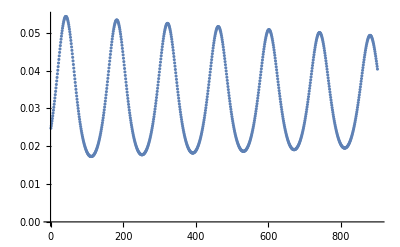

```mathematica
ListPlot[Ftraj,PlotRange->{0,All}]
```

```mathematica
Starvation/.M->10^2
```

0.0000427472

```mathematica
Recovery/.M->10^2
```

7.91067×10^-7

```mathematica
Min[-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ)*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]),0.99]/.values
```

RandomReal::unifr: The endpoints specified by {-PercentPerturbed,PercentPerturbed} for the endpoints of the uniform distribution range are not real valued.

0.261024